```mathematica
ClearAll["Global`*"]
```

```mathematica
table11 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic1_1.txt",{"Table", "Data"}];
table11[[All,1]]=table11[[All,1]]-table11[[1,1]];
table11[[All,2]]=((table11[[All,2]]+0.002)/(0.0043×0.00526));
table11[[All,2]]=table11[[All,2]]-Min[table11[[All,2]]];
```

```mathematica
table12 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic1_2.txt",{"Table", "Data"}];
table12[[All,1]]=table12[[All,1]]-table12[[1,1]];
table12[[All,2]]=((table12[[All,2]]+0.002)/(0.0043×0.00526));
table12[[All,2]]=table12[[All,2]]-Min[table12[[All,2]]]
```

{96.9582,10.611,10.611,2.25484,1.50323,1.37059,1.32638,1.28216,1.23795,1.19374,1.14953,1.10531,1.0611,1.01689,0.972677,0.928464,0.884251,0.840039,0.795826,0.751614,0.707401,0.663189,0.618976,0.574763,0.530551,0.486338,0.442126,0.397913,0.397913,0.353701,0.309488,0.265275,0.221063,0.17685,0.132638,0.0884251,0.0442126,0.,0.}

```mathematica
table13 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic1_3.txt",{"Table", "Data"}];
table13[[All,1]]=table13[[All,1]]-table13[[1,1]];
table13[[All,2]]=((table13[[All,2]]+0.002)/(0.0043×0.00526));
table13[[All,2]]=table13[[All,2]]-Min[table13[[All,2]]];
```

```mathematica
table14 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic1_4.txt",{"Table", "Data"}];
table14[[All,1]]=table14[[All,1]]-table14[[1,1]];
table14[[All,2]]=((table14[[All,2]]+0.002)/(0.0043×0.00526));
table14[[All,2]]=table14[[All,2]]-Min[table14[[All,2]]];
```

```mathematica
table15 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic1_5.txt",{"Table", "Data"}];
table15[[All,1]]=table15[[All,1]]-table15[[1,1]];
table15[[All,2]]=((table15[[All,2]]+0.002)/(0.0043×0.00526));
table15[[All,2]]=table15[[All,2]]-Min[table15[[All,2]]];
```

```mathematica
Export["table11.dat",table11];Export["table12.dat",table12];Export["table13.dat",table13];Export["table14.dat",table14];Export["table15.dat",table15];
```

```mathematica
Directory[]
```

C:\Users\tatki\Documents

```mathematica
T[k_,T0_,Tout_,t_]:=Tout+(T0-Tout)×Exp[-k×t]
```

```mathematica
fit11=FindFit[table11,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→21.371,T0→49.1238,Tout→0.927058}

```mathematica
fit12=FindFit[table12,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→22.5552,T0→96.8298,Tout→0.896051}

```mathematica
fit13=FindFit[table13,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→24.3006,T0→276.808,Tout→0.769746}

```mathematica
fit14=FindFit[table14,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→6.77955,T0→454.146,Tout→-1.82138}

```mathematica
fit15=FindFit[table15,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→24.0746,T0→124.754,Tout→0.616011}

```mathematica
Tset={Tout/.fit11,Tout/.fit12,Tout/.fit13,Tout/.fit14,T0/.fit15}
```

{0.927058,0.896051,0.769746,-1.82138,124.754}

```mathematica
Mean[Tset]
```

25.1052

```mathematica
StandardDeviation[Tset]
```

55.7178

```mathematica
k11=Mean[{k/.fit11,k/.fit12,k/.fit13,k/.fit14,k/.fit15}]
```

19.8162

```mathematica
StandardDeviation[{k/.fit11,k/.fit12,k/.fit13,k/.fit14,k/.fit15}]
```

7.38439

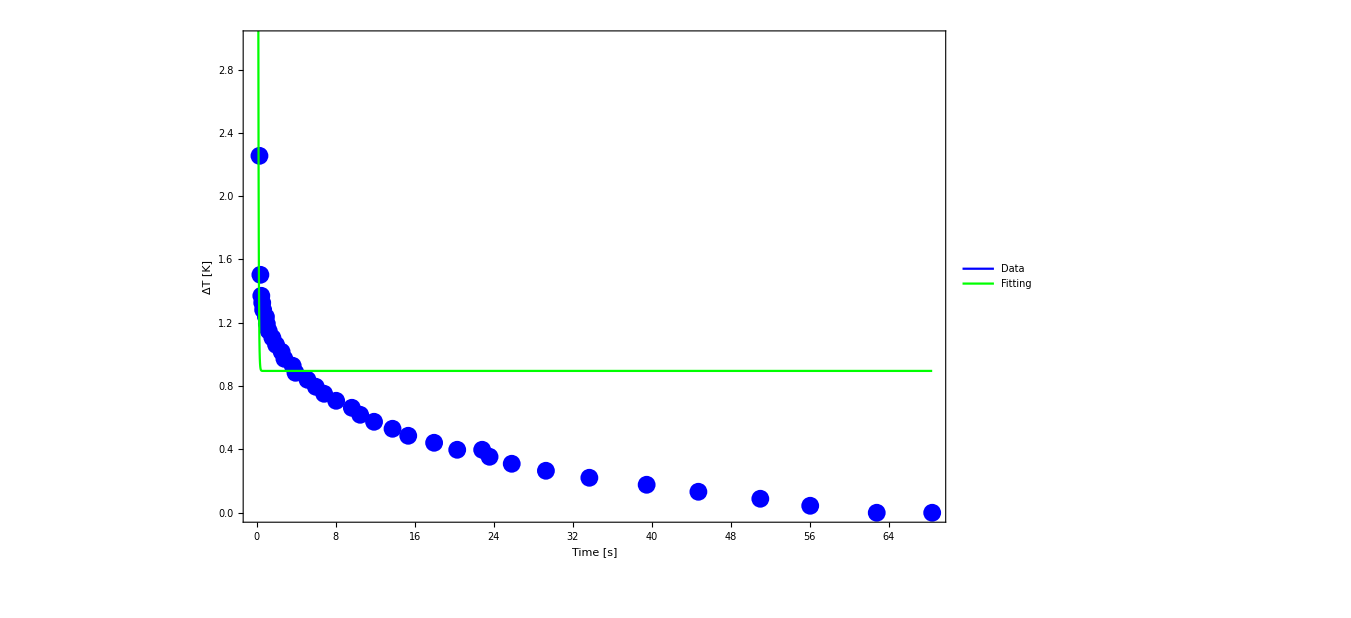

```mathematica
Legended[Show[ListPlot[table12,PlotStyle->Blue],
Plot[T[k,T0,Tout,t]/.fit12,{t,0,Max[table12[[All,1]]]},PlotStyle->Green],  Frame->{True,True,False,False},FrameLabel->{"Time [s]","ΔT [K]"},ImageSize->1000, BaseStyle->{FontSize->24}],LineLegend[{Blue, Green},{"Data", "Fitting"}]]
```